## The heat equation

### DD vs NN homogeneous boundary conditions

#### Homogeneous DD boundary conditions: T1=T2=0

```mathematica
sol//Clear
L=5;
HeatEq={D[u[t,x],t]==k D[u[t,x],{x,2}]};
IC={u[0,x]==Sin[π x/L] E^(-(x-L/2)^2)};
BC={u[t,0]==0,u[t,L]==0};
```

```mathematica
sol=NDSolve[
Join[HeatEq/.k->1/3,BC,IC],
u[t,x],{t,0,10},{x,0,L}];
```

```mathematica
u[t,x]/.%6
```

{InterpolatingFunction[…][t,x]}

```mathematica
Plot3D[Evaluate[u[t,x]/.sol],{t,0,10},{x,0,5}, PlotRange->All,AxesLabel->{t,x,u}]
```

-Graphics3D-

```mathematica
Animate[Plot[u[t,x]/.sol[[1]]/.{t->t1,x->x1},{x1,0,5}, PlotRange->{0,2},AxesLabel->{x,u}],{t1,0,10},AnimationRunning->False]
```

The average temperature drops because contact with the heat bath dissipates/absorbs energy

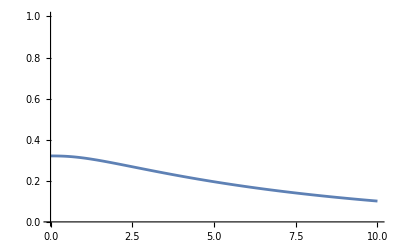

```mathematica
avg[t_]:=NIntegrate[Evaluate[u[t,x]/.sol],{x,0,L}][[1]]
Plot[1/L avg[t],{t,0,10},PlotRange->{0,1}]
```

#### Homogeneous NN boundary conditions

```mathematica
sol//Clear
L=5;
HeatEq={D[u[t,x],t]==k D[u[t,x],{x,2}]};
IC={u[0,x]==Sin[π x/L] E^(-(x-L/2)^2)};
BC={Derivative[0,1][u][t,0]==0,Derivative[0,1][u][t,L]==0};
```

```mathematica
sol=NDSolve[
Join[HeatEq/.k->1/3,BC,IC],
u[t,x],{t,0,10},{x,0,L}];
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

```mathematica
Plot3D[Evaluate[u[t,x]/.sol],{t,0,10},{x,0,5}, PlotRange->All,AxesLabel->{t,x,u}]
```

-Graphics3D-

```mathematica
Animate[Plot[u[t,x]/.sol[[1]]/.{t->t1,x->x1},{x1,0,5}, PlotRange->{0,1},AxesLabel->{x,u}],{t1,0,10},AnimationRunning->False]
```

The average temperature remains constant, by energy conservation

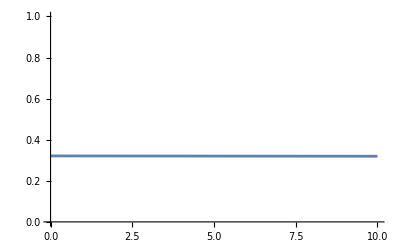

```mathematica
avg[t_]:=NIntegrate[Evaluate[u[t,x]/.sol],{x,0,L}][[1]]
Plot[1/L avg[t],{t,0,10},PlotRange->{0,1}]
```

#### Inhomogeneous DD boundary conditions: T1=1, T2=0

```mathematica
sol//Clear
L=5;
HeatEq={D[u[t,x],t]==k D[u[t,x],{x,2}]};
IC={u[0,x]==Sin[π x/L] E^(-(x-L/2)^2)};
BC={u[t,0]==1,u[t,L]==0};
```

```mathematica
sol=NDSolve[
Join[HeatEq/.k->1/3,BC,IC],
u[t,x],{t,0,10},{x,0,L}];
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

```mathematica
Plot3D[Evaluate[u[t,x]/.sol],{t,0,10},{x,0,5}, PlotRange->All,AxesLabel->{t,x,u}]
```

-Graphics3D-

```mathematica
Animate[Plot[u[t,x]/.sol[[1]]/.{t->t1,x->x1},{x1,0,5}, PlotRange->{0,1},AxesLabel->{x,u}],{t1,0,10},AnimationRunning->False]
```

The average temperature changes because contact with the heat bath dissipates/absorbs energy

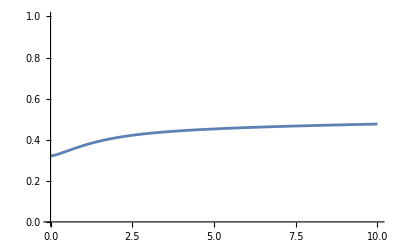

```mathematica
avg[t_]:=Integrate[Evaluate[u[t,x]/.sol],{x,0,L}][[1]]
Plot[1/L avg[t],{t,0,10},PlotRange->{0,1}]
```

### High vs low thermal diffusivity

```mathematica
sol//Clear;
L=5;
HeatEq={D[u[t,x],t]==k D[u[t,x],{x,2}]};
IC={u[0,x]==Sin[π x/L] E^(-(x-L/2)^2)};
BC={u[t,0]==0,u[t,L]==0};
```

```mathematica
solHL[s_]:=NDSolve[
Join[HeatEq/.k->s,BC,IC],
u[t,x],{t,0,10},{x,0,L}];
```

```mathematica
Manipulate[
Plot3D[Evaluate[u[t,x]/.solHL[s]],{t,0,10},{x,0,5}, PlotRange->All,AxesLabel->{t,x,u}]
,{s,0,3}]
```

NDSolve::bcedge: Boundary condition u[t,4.9]==0 is not specified on a single edge of the boundary of the computational domain.

ReplaceAll::reps: {NDSolve[{u^(1,0)[t,x]==1/10 ⅇ^Times[«2»] Sin[Times[«2»]]+2.745 u^(0,2)[t,x],u[t,0.1]==0,u[t,4.9]==0,u[0,x]==u[0,x]==ⅇ^(-Power[«2»]) Sin[(π x)/5]},u[t,x],{t,0,10},{x,0,5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000715 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{u^(1,0)[0.000715,0.0003575]==2.07412×10^-7+2.745 u^(0,2)[0.000715,0.0003575],u[0.000715,0.1]==0,u[0.000715,4.9]==0,u[0,0.0003575]==u[0,0.0003575]==4.34402×10^-7},u[0.000715,0.0003575],{0.000715,0,10},{0.0003575,0,5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000715 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{u^(1,0)[0.000715,0.0003575]==2.07412×10^-7+2.745 u^(0,2)[0.000715,0.0003575],u[0.000715,0.1]==0.,u[0.000715,4.9]==0.,u[0.,0.0003575]==u[0.,0.0003575]==4.34402×10^-7},u[0.000715,0.0003575],{«1»},{0.0003575,0.,5.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.715001 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

### Space-dependent thermal diffusivity

homogeneous NN boundary conditions (insulation).
Heat will spread out. But diffusivity is exactly zero at one end, so it never receives any heat.

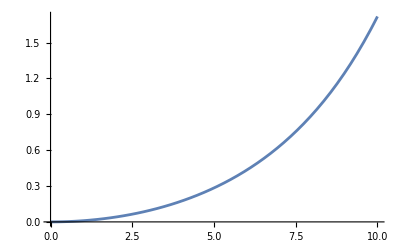

```mathematica
κ[x_]:=(E^(x^2/100)-1);
Plot[κ[x],{x,0,10},PlotRange->All]
```

```mathematica
sol//Clear
L=5;
HeatEq={D[u[t,x],t]==D[κ[x] D[u[t,x],x],x]};
IC={u[0,x]==Sin[π x/L] E^(-(x-L/2)^2)};
BC={Derivative[0,1][u][t,0]==0,Derivative[0,1][u][t,L]==0};
```

```mathematica
sol=NDSolve[
Join[HeatEq,BC,IC],
u[t,x],{t,0,100},{x,0,L}];
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

```mathematica
Plot3D[Evaluate[u[t,x]/.sol],{t,0,50},{x,0,5}, PlotRange->All,AxesLabel->{t,x,u}]
```

-Graphics3D-

```mathematica
Animate[Plot[u[t,x]/.sol[[1]]/.{t->t1,x->x1},{x1,0,5}, PlotRange->{0,1},AxesLabel->{x,u}],{t1,0,50},AnimationRunning->False]
```

Since thermal diffusivity is exactly zero at x=0, nothing happens and the system does not quite thermalize there. Only away from x=0 it evolves towards the equilibrium temperature.

### Time evolution from convexity

DD boundary conditions (thermal baths)
Consider two different initial conditions, with the same diffusivity coefficient. The one with higher curvature decays faster.

```mathematica
sol//Clear
L=5;
HeatEq={D[u[t,x],t]==k D[u[t,x],{x,2}]};
IC1={u[0,x]==Sin[π x/L] E^(-(x-L/2)^2)};
IC2={u[0,x]==Sin[5π x/L]^2 E^(-(x-L/2)^2)};
BC={u[t,0]==0,u[t,L]==0};
```

```mathematica
sol1=NDSolve[
Join[HeatEq/.k->1/3,BC,IC1],
u[t,x],{t,0,10},{x,0,L}];
sol2=NDSolve[
Join[HeatEq/.k->1/3,BC,IC2],
u[t,x],{t,0,10},{x,0,L}];
```

```mathematica
Plot3D[Evaluate[u[t,x]/.sol1],{t,0,10},{x,0,5}, PlotRange->All,AxesLabel->{t,x,u}]
Plot3D[Evaluate[u[t,x]/.sol2],{t,0,10},{x,0,5}, PlotRange->All,AxesLabel->{t,x,u}]
```

-Graphics3D-

-Graphics3D-

```mathematica
Animate[
{
Plot[u[t,x]/.sol1[[1]]/.{t->t1,x->x1},{x1,0,5}, PlotRange->{0,1},AxesLabel->{x,u}],
Plot[u[t,x]/.sol2[[1]]/.{t->t1,x->x1},{x1,0,5}, PlotRange->{0,1},AxesLabel->{x,u}]
},{t1,0,10},AnimationRunning->False]
```

### Inhomogeneous NN boundary conditions (not insulated) with equilibrium

NN boundary conditions: same amount of heat that flows in from one side also exits on the other side

```mathematica
sol//Clear
L=5;
HeatEq={D[u[t,x],t]==k D[u[t,x],{x,2}]};
IC={u[0,x]==L/(2π)Sin[2π x/L] +4 L/(2π)};
BC={Derivative[0,1][u][t,0]==1,Derivative[0,1][u][t,L]==1};
```

```mathematica
sol=NDSolve[
Join[HeatEq/.k->1/3,BC,IC],
u[t,x],{t,0,50},{x,0,L}];
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

```mathematica
Plot3D[Evaluate[u[t,x]/.sol],{t,0,50},{x,0,5}, PlotRange->All,AxesLabel->{t,x,u}]
```

-Graphics3D-

```mathematica
Animate[Plot[u[t,x]/.sol[[1]]/.{t->t1,x->x1},{x1,0,5}, PlotRange->{0,6},AxesLabel->{x,u}],{t1,0,50},AnimationRunning->False]
```

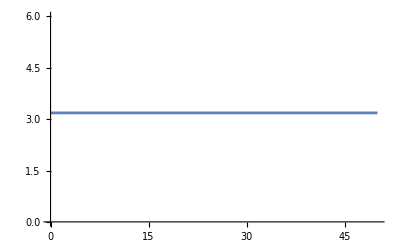

```mathematica
avg[t_]:=1/L NIntegrate[Evaluate[u[t,x]/.sol],{x,0,L}][[1]]
Plot[avg[t],{t,0,50},PlotRange->{0,6}]
```

Eventually the system reaches a steady equilibrium state, where temperature has a constant gradient, signaling a steady heat flow.

### Inhomogeneous NN boundary conditions (not insulated) without equilibrium

NN boundary conditions: net negative heat influx

```mathematica
sol//Clear
L=5;
HeatEq={D[u[t,x],t]==k D[u[t,x],{x,2}]};
IC={u[0,x]==L/(2π)Sin[π x/L]+3 };
BC={Derivative[0,1][u][t,0]==-1,Derivative[0,1][u][t,L]==1};
```

```mathematica
sol=NDSolve[
Join[HeatEq/.k->1/3,BC,IC],
u[t,x],{t,0,50},{x,0,L}];
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

```mathematica
Plot3D[Evaluate[u[t,x]/.sol],{t,0,10},{x,0,5}, PlotRange->All,AxesLabel->{t,x,u}]
```

-Graphics3D-

```mathematica
Animate[Plot[u[t,x]/.sol[[1]]/.{t->t1,x->x1},{x1,0,5}, PlotRange->{0,6},AxesLabel->{x,u}],{t1,0,50},AnimationRunning->False]
```

Eventually the system does NOT reach a steady equilibrium state. 
The average temperature keeps decreasing because the net heat flow is negative.

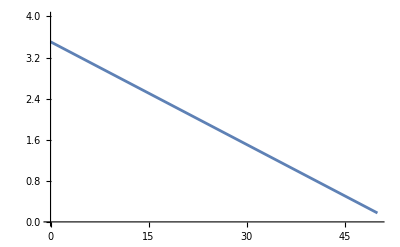

```mathematica
avg[t_]:=1/L NIntegrate[Evaluate[u[t,x]/.sol],{x,0,L}][[1]]
Plot[avg[t],{t,0,50},PlotRange->{0,4}]
```

### NN homogeneous boundary conditions with source

homogeneous NN boundary conditions (insulation)
initial condition: zero temperature
time-independent gaussian source centered at x=L/2

```mathematica
sol//Clear
L=5;
HeatEq={D[u[t,x],t]==k D[u[t,x],{x,2}]+ q[x]}/.{q[x]->1/10 E^(-(x-L/2)^2)};
IC={u[0,x]==0};
BC={Derivative[0,1][u][t,0]==0,Derivative[0,1][u][t,L]==0};
```

```mathematica
sol=NDSolve[
Join[HeatEq/.k->1/10,BC,IC],
u[t,x],{t,0,10},{x,0,L}];
```

```mathematica
Plot3D[Evaluate[u[t,x]/.sol],{t,0,10},{x,0,5}, PlotRange->All,AxesLabel->{t,x,u}]
```

-Graphics3D-

```mathematica
Animate[Plot[u[t,x]/.sol[[1]]/.{t->t1,x->x1},{x1,0,5}, PlotRange->{0,0.8},AxesLabel->{x,u}],{t1,0,10},AnimationRunning->False]
```

There is no equilibrium, since the source keeps pumping in heat.
The average temperature keeps increasing because the net heat flow is negative.

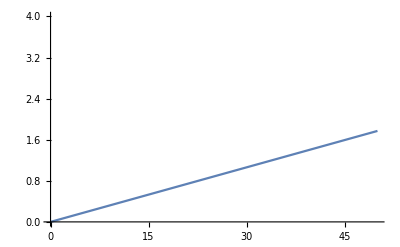

```mathematica
avg[t_]:=1/L Integrate[Evaluate[u[t,x]/.sol],{x,0,L}][[1]]
Plot[avg[t],{t,0,50},PlotRange->{0,4}]
```

Since the source pumps energy at constant rate (time-independent), the energy grows linearly.

Now consider a variant where the thermal diffusivity is much higher: set k=10.
Heat spreads out immediately throughout the material, which heats up almost uniformly.

```mathematica
sol=NDSolve[
Join[HeatEq/.k->10,BC,IC],
u[t,x],{t,0,10},{x,0,L}];
```

```mathematica
Plot3D[Evaluate[u[t,x]/.sol],{t,0,10},{x,0,5}, PlotRange->All,AxesLabel->{t,x,u}]
```

-Graphics3D-

```mathematica
Animate[Plot[u[t,x]/.sol[[1]]/.{t->t1,x->x1},{x1,0,5}, PlotRange->{0,0.8},AxesLabel->{x,u}],{t1,0,10},AnimationRunning->False]
```

### NN homogeneous boundary conditions with time-dependent source

homogeneous NN boundary conditions (insulation)
initial condition: zero temperature
time dependent (oscillating) gaussian source centered at x=L/2

```mathematica
sol//Clear
L=5;
HeatEq={D[u[t,x],t]==k D[u[t,x],{x,2}]+ q[t,x]}/.{q[t,x]->1/10 E^(-(x-L/2)^2)Sin[1.5t]};
IC={u[0,x]==0};
BC={Derivative[0,1][u][t,0]==0,Derivative[0,1][u][t,L]==0};
```

```mathematica
sol=NDSolve[
Join[HeatEq/.k->1/15,BC,IC],
u[t,x],{t,0,100},{x,0,L}];
```

```mathematica
Plot3D[Evaluate[u[t,x]/.sol],{t,0,10},{x,0,5}, PlotRange->All,AxesLabel->{t,x,u}]
```

-Graphics3D-

```mathematica
Animate[Plot[u[t,x]/.sol[[1]]/.{t->t1,x->x1},{x1,0,5}, PlotRange->{-0.1,0.15},AxesLabel->{x,u}],{t1,0,30},AnimationRunning->False]
```

There is no equilibrium, since the source keeps pumping heat in and then out
The average temperature oscillates

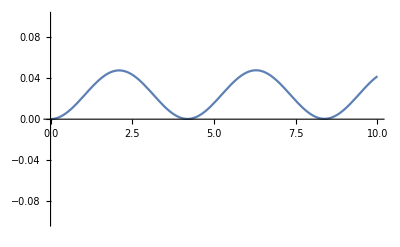

```mathematica
avg[t_]:=1/L NIntegrate[Evaluate[u[t,x]/.sol],{x,0,L}][[1]]
Plot[avg[t],{t,0,10},PlotRange->{-0.1,0.1}]
```

Now a variant with higher k.
If the thermal diffusivity is small (as before) only the region near the source feels the oscillations.
But with larger thermal diffusivity the heat pumped in/out spread out much faster, and are felt also near the boundary.

```mathematica
sol=NDSolve[
Join[HeatEq/.k->1,BC,IC],
u[t,x],{t,0,10},{x,0,L}];
```

```mathematica
Plot3D[Evaluate[u[t,x]/.sol],{t,0,10},{x,0,5}, PlotRange->All,AxesLabel->{t,x,u}]
```

-Graphics3D-

```mathematica
Animate[Plot[u[t,x]/.sol[[1]]/.{t->t1,x->x1},{x1,0,5}, PlotRange->{-0.1,0.15},AxesLabel->{x,u}],{t1,0,10},AnimationRunning->False]
```

```mathematica
sol=NDSolve[
Join[HeatEq/.k->10,BC,IC],
u[t,x],{t,0,10},{x,0,L}];
```

```mathematica
Plot3D[Evaluate[u[t,x]/.sol],{t,0,10},{x,0,5}, PlotRange->All,AxesLabel->{t,x,u}]
```

-Graphics3D-

```mathematica
Animate[Plot[u[t,x]/.sol[[1]]/.{t->t1,x->x1},{x1,0,5}, PlotRange->{-0.1,0.15},AxesLabel->{x,u}],{t1,0,10},AnimationRunning->False]
```

### Temperature profile with DD boundary conditions in 1d, 2d, 3d

Homogeneous DD (thermal bath), same thermal diffusivity.
For 2d and 3d consider the radial direction (symmetric in angular directions)

```mathematica
sol//Clear
L=5;
HeatEq1d={D[u[t,x],t]==k D[u[t,x],{x,2}]};
HeatEq2d={D[u[t,x],t]==k 1/x D[ x D[u[t,x],x],x]};
HeatEq3d={D[u[t,x],t]==k 1/x^2 D[ x^2 D[u[t,x],x],x]};
δ=0.1;
IC={u[0,x]==u[0,x]==Sin[π x/L] E^(-(x-L/2)^2)};
BC1d={u[t,δ]==0,u[t,L-δ]==0};
BC2d={u[t,L-δ]==0};
BC3d={u[t,L-δ]==0};
```

```mathematica
sol1d=NDSolve[
Join[HeatEq1d/.k->1/3,BC1d,IC],
u[t,x],{t,0,10},{x,δ,L-δ}];
sol2d=NDSolve[
Join[HeatEq2d/.k->1/3,BC2d,IC],
u[t,x],{t,0,10},{x,δ,L-δ}];
sol3d=NDSolve[
Join[HeatEq3d/.k->1/3,BC3d,IC],
u[t,x],{t,0,10},{x,δ,L-δ}];
```

NDSolve::femcscd: The PDE is convection dominated and the result may not be stable. Adding artificial diffusion may help.

```mathematica
{
Plot3D[Evaluate[u[t,x]/.sol1d],{t,0,10},{x,δ,L-δ}, PlotRange->All,AxesLabel->{t,x,u}],
Plot3D[Evaluate[u[t,x]/.sol2d],{t,0,10},{x,δ,L-δ}, PlotRange->All,AxesLabel->{t,x,u}],
Plot3D[Evaluate[u[t,x]/.sol3d],{t,0,10},{x,δ,L-δ}, PlotRange->All,AxesLabel->{t,x,u}]
}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Manipulate[
{
Plot[u[t,x]/.sol1d[[1]]/.{t->t1,x->x1},{x1,δ,L-δ}, PlotRange->{0,1},AxesLabel->{x,u},PlotLabel->"1d"],
Plot[u[t,x]/.sol2d[[1]]/.{t->t1,x->x1},{x1,δ,L-δ}, PlotRange->{0,1},AxesLabel->{x,u},PlotLabel->"2d"],
Plot[u[t,x]/.sol3d[[1]]/.{t->t1,x->x1},{x1,δ,L-δ}, PlotRange->{0,1},AxesLabel->{x,u},PlotLabel->"3d"]
},
{t1,0,10}]
```

What is the difference in behaviour of the three cases? Can you explain why this happens, both physically and mathematically?